```mathematica
(* Loess regression. Span selection *)
(* 1. Toy example: *)
RandomSeed[4];
```

```mathematica
x = RandomVariate[NormalDistribution[], 500];
```

```mathematica
y = x^3+(x-3)^2+(x-8)-1+RandomVariate[NormalDistribution[0, 1/2],500] ;
```

```mathematica
df=MapThread[{#1, #2}&,{x, y}];
```

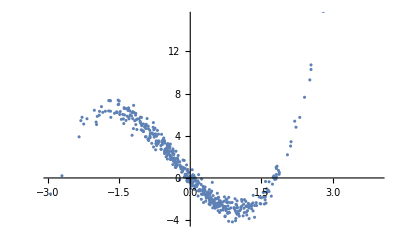

```mathematica
ListPlot[df]
```

```mathematica
(* 2. Set up cross validation loop: *)
spanSeq=Range[0.01, 0.5, 0.01];
```

```mathematica
k=10;
```

```mathematica
RandomSeed[1];
```

```mathematica
folds = RandomChoice[Range[k], Length[x]];
```

```mathematica
cvErrorMtrx = ConstantArray["NA", {Length[spanSeq], k}];
cvErrorMtrx//MatrixForm
```

(NA | NA | NA | NA | NA | NA | NA | NA | NA | NA
NA | NA | NA | NA | NA | NA | NA | NA | NA | NA
NA | NA | NA | NA | NA | NA | NA | NA | NA | NA
NA | NA | NA | NA | NA | NA | NA | NA | NA | NA
NA | NA | NA | NA | NA | NA | NA | NA | NA | NA
NA | NA | NA | NA | NA | NA | NA | NA | NA | NA
NA | NA | NA | NA | NA | NA | NA | NA | NA | NA
NA | NA | NA | NA | NA | NA | NA | NA | NA | NA
NA | NA | NA | NA | NA | NA | NA | NA | NA | NA
NA | NA | NA | NA | NA | NA | NA | NA | NA | NA
NA | NA | NA | NA | NA | NA | NA | NA | NA | NA
NA | NA | NA | NA | NA | NA | NA | NA | NA | NA
NA | NA | NA | NA | NA | NA | NA | NA | NA | NA
NA | NA | NA | NA | NA | NA | NA | NA | NA | NA
NA | NA | NA | NA | NA | NA | NA | NA | NA | NA
NA | NA | NA | NA | NA | NA | NA | NA | NA | NA
NA | NA | NA | NA | NA | NA | NA | NA | NA | NA
NA | NA | NA | NA | NA | NA | NA | NA | NA | NA
NA | NA | NA | NA | NA | NA | NA | NA | NA | NA
NA | NA | NA | NA | NA | NA | NA | NA | NA | NA
NA | NA | NA | NA | NA | NA | NA | NA | NA | NA
NA | NA | NA | NA | NA | NA | NA | NA | NA | NA
NA | NA | NA | NA | NA | NA | NA | NA | NA | NA
NA | NA | NA | NA | NA | NA | NA | NA | NA | NA
NA | NA | NA | NA | NA | NA | NA | NA | NA | NA
NA | NA | NA | NA | NA | NA | NA | NA | NA | NA
NA | NA | NA | NA | NA | NA | NA | NA | NA | NA
NA | NA | NA | NA | NA | NA | NA | NA | NA | NA
NA | NA | NA | NA | NA | NA | NA | NA | NA | NA
NA | NA | NA | NA | NA | NA | NA | NA | NA | NA
NA | NA | NA | NA | NA | NA | NA | NA | NA | NA
NA | NA | NA | NA | NA | NA | NA | NA | NA | NA
NA | NA | NA | NA | NA | NA | NA | NA | NA | NA
NA | NA | NA | NA | NA | NA | NA | NA | NA | NA
NA | NA | NA | NA | NA | NA | NA | NA | NA | NA
NA | NA | NA | NA | NA | NA | NA | NA | NA | NA
NA | NA | NA | NA | NA | NA | NA | NA | NA | NA
NA | NA | NA | NA | NA | NA | NA | NA | NA | NA
NA | NA | NA | NA | NA | NA | NA | NA | NA | NA
NA | NA | NA | NA | NA | NA | NA | NA | NA | NA
NA | NA | NA | NA | NA | NA | NA | NA | NA | NA
NA | NA | NA | NA | NA | NA | NA | NA | NA | NA
NA | NA | NA | NA | NA | NA | NA | NA | NA | NA
NA | NA | NA | NA | NA | NA | NA | NA | NA | NA
NA | NA | NA | NA | NA | NA | NA | NA | NA | NA
NA | NA | NA | NA | NA | NA | NA | NA | NA | NA
NA | NA | NA | NA | NA | NA | NA | NA | NA | NA
NA | NA | NA | NA | NA | NA | NA | NA | NA | NA
NA | NA | NA | NA | NA | NA | NA | NA | NA | NA
NA | NA | NA | NA | NA | NA | NA | NA | NA | NA)

```mathematica
(* Use Loess: *)
Loess=.
LoessR=ResourceFunction["Loess"]
```

```mathematica
(* 3. Nested for loop *)
maxDist=Max[df[[All, 1]]]-Min[df[[All, 1]]]/2;
For[i=1,i<=Length[spanSeq],i++,For[j=1, j<= k, j++,{
fit =df[[Select[Range[Length[df]], folds[[#]]!= j&]]];
pred=df[[Select[Range[Length[df]], folds[[#]]== j&]]];
preds = LoessR[fit, Scaled[spanSeq[[i]]], pred[[All, 1]], {InterpolationOrder-> 2,"WeightsFunction"-> ((1-(Norm[#]/maxDist)^3)^3&) }];
cvErrorMtrx[[i]][[j]]=Mean[(pred[[All, 2]]-preds)^2];
}]]
```

```mathematica
(* 4. Calculate cross-validation mean square error for each fold: *)
cvErrors=Map[Mean, cvErrorMtrx]
```

{0.97655,0.421351,0.324352,0.299754,0.31088,0.377111,0.39025,0.394888,0.401087,0.403728,0.41905,0.39667,0.4061,0.387103,0.38511,0.394,0.4074,0.411889,0.419234,0.429315,0.455354,0.467622,0.469413,0.482171,0.499384,0.51519,0.531082,0.539452,0.549558,0.564677,0.581023,0.603419,0.616215,0.616441,0.630561,0.646248,0.658384,0.664639,0.677264,0.693847,0.702899,0.71504,0.725223,0.747835,0.764713,0.780757,0.800628,0.817022,0.838908,0.852078}

```mathematica
bestSpanIndex=SortBy[Table[{i, cvErrors[[i]]},{i, 1, Length[cvErrors]}], Last][[1]][[1]]
```

4

```mathematica
bestSpan=spanSeq[[bestSpanIndex]]
```

0.04

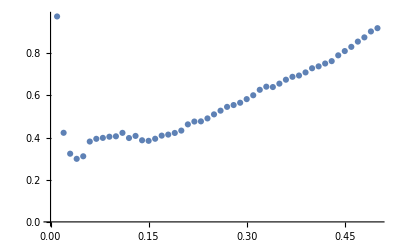

```mathematica
(* Plot results: *)
ListPlot[MapThread[{#1, #2}&, {spanSeq, cvErrors}]]
```

```mathematica
bestFit = LoessR[df, Scaled[bestSpan], df[[All, 1]]];
```

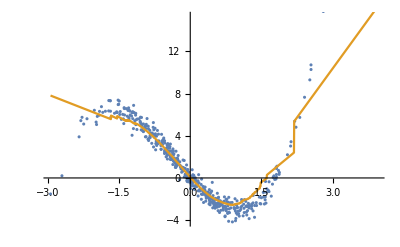

```mathematica
Show[ListPlot[df],   ListLinePlot[{{{0,0}},Table[{x, LoessR[df, Scaled[bestSpan], x]}, {x, Min[df[[All, 1]]], Max[df[[All, 1]]], .005}]}]]
```

```mathematica
bestSpan
```

0.09